# Multiple Linear Regression - Predicting Body Fat

## Mathematica for Research

## Introduction

The dataset contains estimates of the percentage of body fat determined by various body circumference measurements and underwater weight for 252 men. As an accurate measurement of body fat is costly and it is desirable to have an easy solution for estimating body fat. The algorithm used here will be multiple linear regression where the target variable will be body fat and various body circumference measurements will be the prediction variables.

## Familiarising Dataset

The dataset consist of 252 rows which is the estimate of body fat for 252 men by taking account of  various body circumference measurements and underwater weight. In total there will be 15 columns where body fat will be our target variable and others are predictor variable.

### Variables

The variables in the dataset are list below:

Density					                Density determined from underwater weighing

Body Fat (Target variable)			Calculated percent body fat

Age (years)

Weight (lbs)

Height (inches)

Neck circumference (cm)

Chest circumference (cm)

Abdomen 2 circumference (cm)

Hip circumference (cm)

Thigh circumference (cm)

Knee circumference (cm)

Ankle circumference (cm)

Biceps (extended) circumference (cm)

Forearm circumference (cm)

Wrist circumference (cm)

## Data Import & Wrangling

### Reading dataset

```mathematica
bodyFatData=Import["D:\Study\Mathematica\WorkArea\MainProject\Bodyfat.csv",{"CSV","Dataset"},"HeaderLines"->1]
```

Dataset[<>]

### Checking for missing and abnormal data

```mathematica
bodyFatData[Count[_Missing]] (* Checking for missing data *)
```

0

The dataset consist of no missing data hence its good to go.

```mathematica
predictorVariables = {"Density", "Age", "Weight", "Height", "Neck", "Chest", "Abdomen", "Hip", "Thigh", "Knee", "Ankle", "Biceps", "Forearm", "Wrist"};
```

### Test and train data

We have 252 rows in the dataset, so we can split 90 percent of data as the training and remaining 10 percent as test data.

```mathematica
trainData = bodyFatData[0;; 232];
trainDataY = trainData[All,{"bodyfat"}] ;
trainDataX = trainData[All,predictorVariables] ;
```

```mathematica
testData = bodyFatData[233;;252];  
testDataY = testData[All,{"bodyfat"}] ;
testDataX = testData[All,predictorVariables] ;
```

```mathematica
trainDataX
```

Dataset[<>]

### Histogram View (Checking skewness in variables)

```mathematica
pltDensity = Histogram[trainDataX[All, "Density"] // Normal, PlotLabel-> "Density"];
pltAge = Histogram[trainDataX[All, "Age"] // Normal, PlotLabel-> "Age"];
pltWeight = Histogram[trainDataX[All, "Weight"] // Normal, PlotLabel-> "Weight"];
pltHeight = Histogram[trainDataX[All, "Height"] // Normal, PlotLabel-> "Height"];
pltNeck = Histogram[trainDataX[All, "Neck"] // Normal, PlotLabel-> "Neck"];
pltChest = Histogram[trainDataX[All, "Chest"] // Normal, PlotLabel-> "Chest"];
pltAbdomen = Histogram[trainDataX[All, "Abdomen"] // Normal, PlotLabel-> "Abdomen"];
pltHip = Histogram[trainDataX[All, "Hip"] // Normal, PlotLabel-> "Hip"];
pltThigh = Histogram[trainDataX[All, "Thigh"] // Normal, PlotLabel-> "Thigh"];
pltKnee = Histogram[trainDataX[All, "Knee"] // Normal, PlotLabel-> "Knee"];
pltAnkle = Histogram[trainDataX[All, "Ankle"] // Normal, PlotLabel-> "Ankle"];
pltBiceps = Histogram[trainDataX[All, "Biceps"] // Normal, PlotLabel-> "Biceps"];
pltForearm = Histogram[trainDataX[All, "Forearm"] // Normal, PlotLabel-> "Forearm"];
pltWrist= Histogram[trainDataX[All, "Wrist"] // Normal, PlotLabel-> "Wrist"];
pltBodyFat = Histogram[trainDataY[All, "bodyfat"] // Normal, PlotLabel-> "Body Fat (target)"];
```

CorrelationTest::invbvtd: The argument Dataset[«232»] at position 1 should be a matrix of real numbers of dimension 2 with length greater than 2.

CorrelationTest[Dataset[<>]]

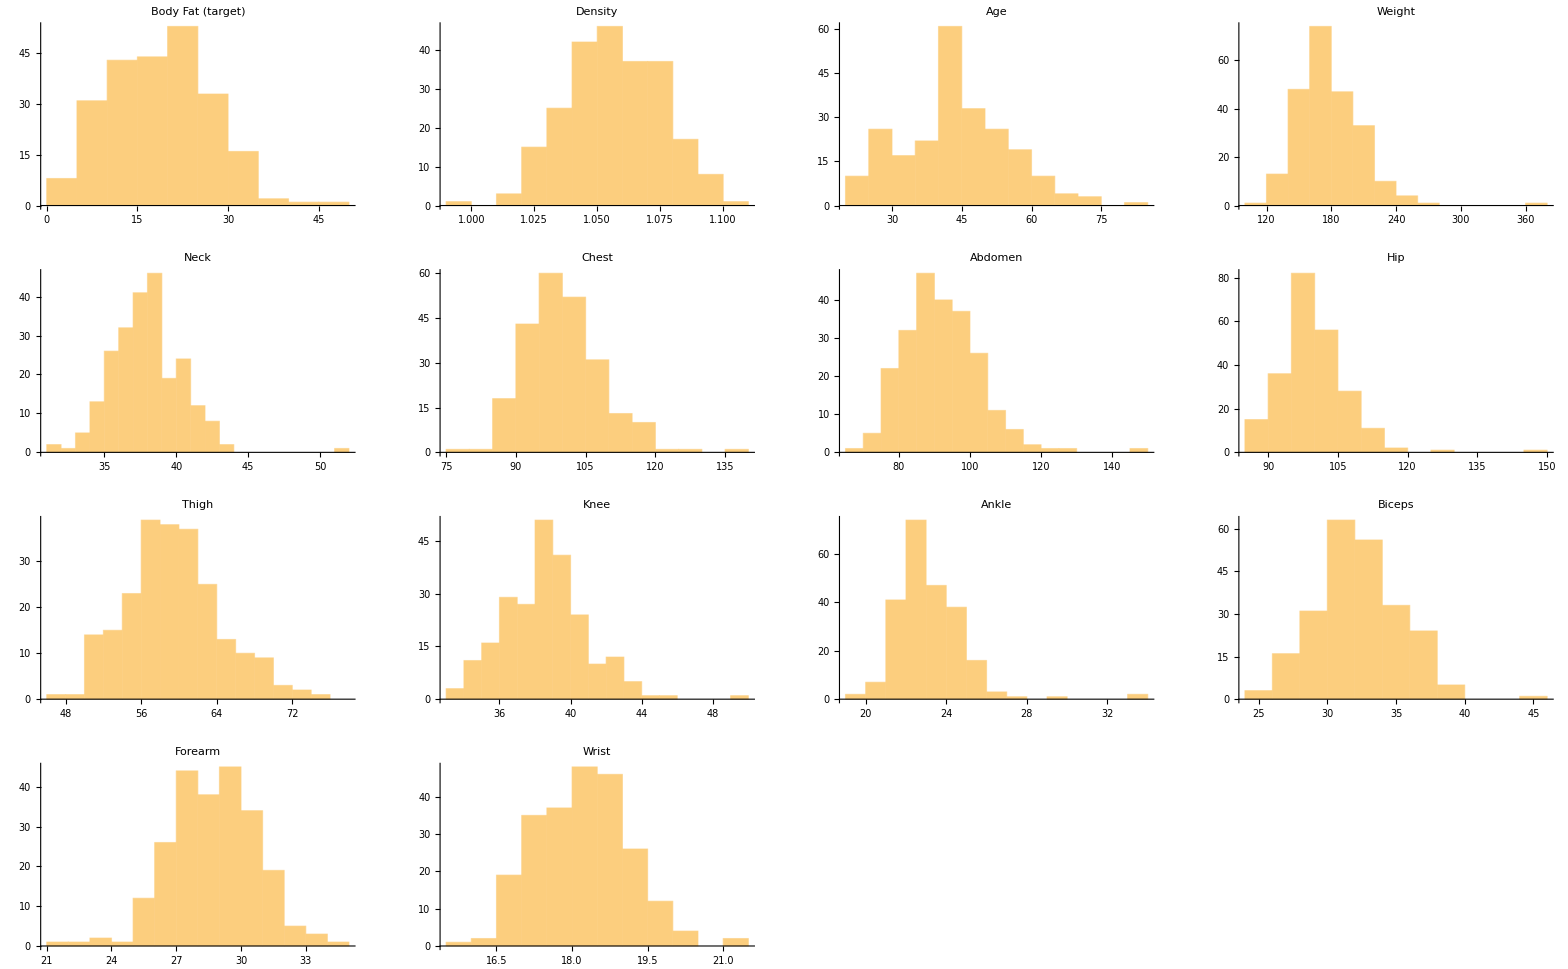

```mathematica
GraphicsGrid[{{pltBodyFat,pltDensity, pltAge, pltWeight},
                           {pltNeck,pltChest, pltAbdomen, pltHip},
                           {pltThigh,pltKnee, pltAnkle, pltBiceps},
                           {pltForearm,pltWrist}
                            }, AspectRatio->1, ImageSize->Full]
```

Inference: Analysing the histograms there is not much skewness in data, even though there is  a lot of outlier values in Ankle, Neck, Abdomen, weight. So by removing that we will get much more cleaner histograms.
If these outliers are significant during modelling we can remove that from. So, as if for now we can keep the data.